## Load files with data

```mathematica
elements={"u235"(*,"pu239"*)};
plotNames={"1s","1minute","1hour",(*"24hours",*)"1week","1year","CFY"};
forPlot={};
```

```mathematica
For[i=1,i≤Length@elements,i++,
filenames =FileNameJoin[{NotebookDirectory[],elements[[i]]<>"time"<>#<>".dat"}]&/@plotNames;
data=Import[#,"Data"]&/@filenames;
AppendTo[forPlot,elements[[i]]->data]
]
(*maximumData=Import[FileNameJoin[{NotebookDirectory[],"maximum_time.dat"}],"Data"];*)
```

## Neutrino spectrum plots

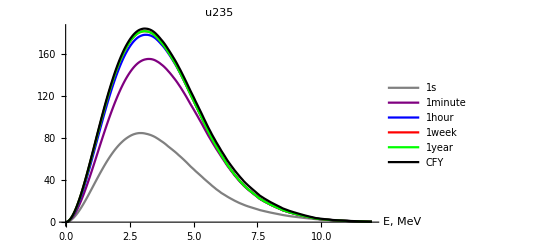

```mathematica
ListPlot[forPlot[[1,2]],PlotStyle->{Gray,Purple,Blue,Red,Green,Black},AxesLabel->{"E, MeV"},Joined->True,PlotLegends->plotNames,
PlotRange->{{0,12},Automatic},PlotLabel->forPlot[[1,1]]]
(*ListPlot[forPlot[[2,2]],PlotStyle->{Gray,Purple,Blue,Red,Green},AxesLabel->{"E, MeV"},Joined->True,(*PlotLegends->plotNames,*)
PlotRange->{{0,12},Automatic},PlotLabel->forPlot[[2,1]]]*)
```

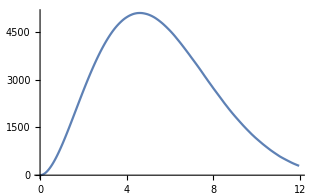

```mathematica
ListPlot[forPlot[[1,2,6]],Joined->True]
```

```mathematica
pos1year=Position[plotNames,"1year"][[1,1]];
u235year=forPlot[[1,2,pos1year]];
pu239year=forPlot[[2,2,pos1year]];
ratio=u235year[[All,2]]/pu239year[[All,2]];
ratioPlot={};
For[i=2,i≤Length@ratio,i++,AppendTo[ratioPlot,{u235year[[i,1]],ratio[[i]]}]]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

```mathematica
ratioPlot;
```

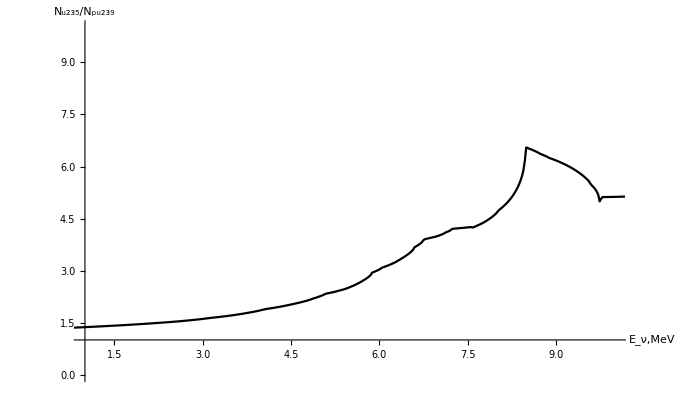

```mathematica
ListPlot[ratioPlot,PlotRange->{{1,10},{0,10}},AxesOrigin->{1,1},Joined->True,AxesLabel->{"E_ν,MeV","N_u235/N_pu239"},PlotStyle->Black]
```

## Normalized plots

```mathematica
dataNormalized={};
data=forPlot[[1,2]];
For[i=1,i≤Length@data,i++,
AppendTo[dataNormalized,
{#[[1]],#[[2]]/Max[data[[i]][[All,2]]]}&/@data[[i]]
]
]
```

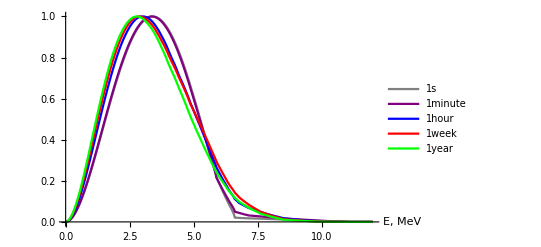

```mathematica
ListPlot[dataNormalized,PlotStyle->{Gray,Purple,Blue,Red,Green},AxesLabel->{"E, MeV"},Joined->True,PlotLegends->plotNames]
```

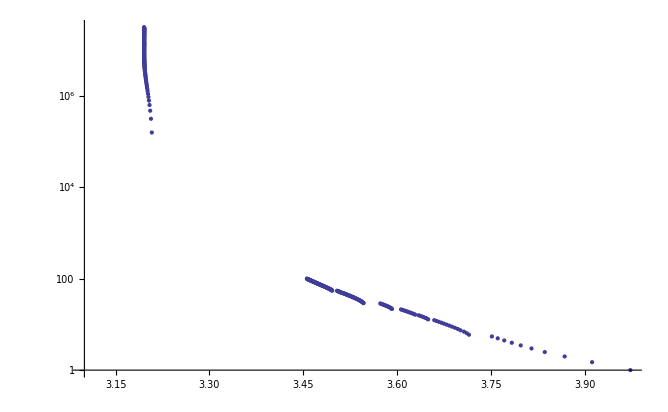

```mathematica
ListLogPlot[maximumData,PlotRange->All,AxesOrigin->{3.1,0}]
```